# LatTest Mathematica Review

This is my Mathematica review notebook.  Extracted from Workshops and SampleLabTest.
For the source code on GitHub,  click here.

## 1. Mathematica Basics

### 创建和访问list:

```mathematica
x = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
x[[3]]
```

3

```mathematica
x[[1;;3]]
```

{1,2,3}

### 迭代器:

```mathematica
Table[x^2, {x, 10}]
```

{1,4,9,16,25,36,49,64,81,100}

### 赋值：

```mathematica
x = 7
```

7

## 2. Workshop2

Question 1.2.1 : Sampling without replacement.

10000行代码中有30行可以被改进，抽取10行代码

```mathematica
(*1行代码需要被改进的概率*)
Binomial[10000, 10]
Binomial[30, 1] * Binomial[10000 - 30, 9] / Binomial[10000, 10]
N[%, 18]
```

2743355077591282538231819720749000

2143751464028247883152007617/73351740042547661450048655635

0.029225638857166378

```mathematica
(*0行代码需要被改进的概率*)
Binomial[30, 0] * Binomial[10000 - 30, 10] / Binomial[10000, 10]
N[%]
(*使用%将结果转化为分数*)
```

1016852777770732245908435612997/1047882000607823735000695080500

0.970389

使用内置的HypergeometricDistribution函数直接计算

```mathematica
PDF[HypergeometricDistribution[10, 30, 10000], 1]
N[%]
```

2143751464028247883152007617/73351740042547661450048655635

0.0292256

使用DiscretePlot命令来打印Hypergeometric的概率

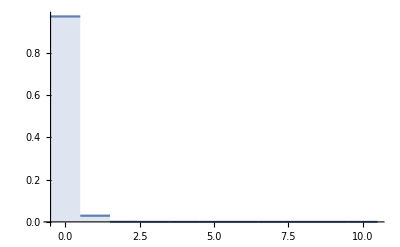

```mathematica
DiscretePlot[PDF[HypergeometricDistribution[10, 30, 10000], k], {k, 0, 10},PlotRange->Full, ExtentSize->1]
```

Now suppose that total number of lines of code from which the sample of size 10 is taken is (a) 1000, (b) 100 or (c) 50, whilst the total number of improvable lines of code remains the same at 30. Alter your command to permit, the probabilities for each of (a), (b) and (c) to be plotted on the one plot. Comment on the differences between the probabilities.

```mathematica
(*从N个中选10个，其中有k行代码需要被改进的概率的PDF，
这里同时生成3个超几何分布，分别是N为1000，500和50*)
Table[PDF[HypergeometricDistribution[10, 30, N], k], {N, {1000, 100, 50}}]
```

{Piecewise[{{(Binomial[30,k] Binomial[970,10-k])/263409560461970212832400, 0≤k≤10}, {0, True}}],Piecewise[{{(Binomial[30,k] Binomial[70,10-k])/17310309456440, 0≤k≤10}, {0, True}}],Piecewise[{{(Binomial[20,10-k] Binomial[30,k])/10272278170, 0≤k≤10}, {0, True}}]}

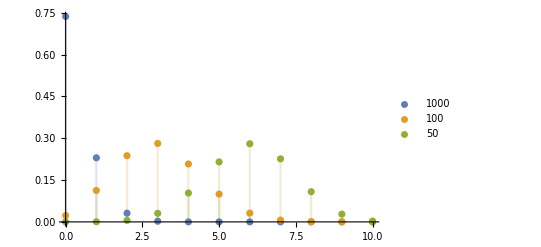

```mathematica
DiscretePlot[Evaluate[%], {k, 0, 10}, PlotRange->Full, PlotLegends->{1000, 100, 50}]
```

Question 1.2.2: Bayes Theorem - Sampling Without Replacement

Given an observed number of 5 lines of code that could be improved in the 20 samples, the total number of lines of code that could be improved out of 1000 was 0, 1, 2, ..., 1000. Plot these probabilities.

```mathematica
(* prior 先验概率, Join命令将两个list合并，先验概率的和需要相加为1，
有1001个值. Joint是先验概率和likelihood的乘积*)
Short[prior = Join[Table[0.9/101, 101], Table[0.1/900, 900]]]

Short[joint = prior * Evaluate[Table[PDF[HypergeometricDistribution[20, i, 1000], 5], {i, 0, 1000}]]]
```

{0.00891089,0.00891089,0.00891089,0.00891089,«993»,0.000111111,0.000111111,0.000111111,0.000111111}

{0.,0.,0.,0.,0.,1.67454×10^-11,9.89578×10^-11,3.41126×10^-10,8.95927×10^-10,1.98535×10^-9,«981»,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*conditional ，根据贝叶斯定理得到的条件概率*)
Short[conditional = joint / Total[joint]]
```

{0.,0.,0.,0.,0.,1.49743×10^-9,8.84913×10^-9,3.05046×10^-8,8.01167×10^-8,1.77537×10^-7,«981»,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Question 1.3 Binomial Probabilities

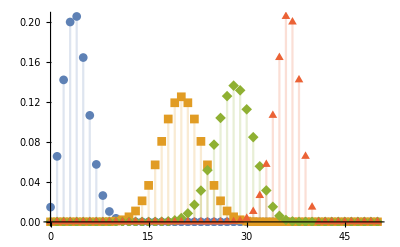

```mathematica
Table[PDF[BinomialDistribution[40, p], k], {p, {0.1, 0.5, 0.7, 0.9}}];
DiscretePlot[Evaluate[%], {k, 0, 50}, PlotMarkers->Automatic, PlotRange->Full]
```

## Workshop3

Question 1

17个球标着输3个球标赢，轮流拿球，不放回，拿到第三个标记为赢的球的获胜. 
a. 如果你先拿，求你第二次拿就赢了的概率 （前三个拿的全是赢）

```mathematica
PDF[HypergeometricDistribution[3, 3, 20], 3]
```

1/1140

b. 如果你先拿，求你对家第二次拿球赢了的概率

```mathematica
PDF[HypergeometricDistribution[3, 3, 20], 2] * 1 / 17
```

1/380

c. 如果你先拿，你赢的概率

```mathematica
Sum[PDF[HypergeometricDistribution[2k, 3, 20], 2] * 1 / (20 - 2k), {k, 1, 9}]
```

35/76

d. 如果你第二个拿，你赢的概率

```mathematica
Sum[PDF[HypergeometricDistribution[2k+1, 3, 20], 2] * 1 / (19 - 2k), {k, 1, 9}]
```

41/76

Question 2

100 fuses there are 20 defective ones. A sample of 5 fuses are randomly selected from the lot without replacement. Let X be the number of defective fuses found in the example
a. Find P(X = 0).
b. Cumulative probability P(X≤3)
c. Mean of X, E(X)
d. Second Moment of X, E(X^2)
e. Variance of X, Var(X)
f. Probability bar graph for PMF of X

0.319309

0.994646

1

1

175/99

76/99

76/99

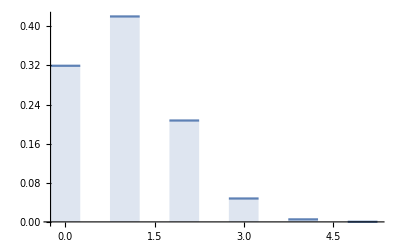

```mathematica
(*a*)
PDF[HypergeometricDistribution[5, 20, 100], 0];
N[%]
(*b*)
CDF[HypergeometricDistribution[5, 20, 100], 3];
N[%]
(*c 两种方法*)
mu = Mean[HypergeometricDistribution[5, 20, 100]]
Expectation[X, X \[Distributed] HypergeometricDistribution[5, 20, 100]]
(*d*)
ex2 = Expectation[X^2, X \[Distributed] HypergeometricDistribution[5, 20, 100]]
(*e 两种方法*)
ex2 - mu^2
Variance[HypergeometricDistribution[5, 20, 100]]
(*f*)
DiscretePlot[PDF[HypergeometricDistribution[5, 20, 100], k], {k, 0, 5}, ExtentSize->0.5]
```

## Workshop 6

Question 1

Suppose X1 ~ N(3, 4), X2~N(3, 4), X1 and X2 are independent.
a. Find MGF of X1 and X2
b. Let Y = 5X1 - 2X2 + 6, Find the MFG of Y
c. Name the distribution Y and give the values of the associated parameters.   Answer: Y~N(15, 58)

```mathematica
(*注意: 在这个垃圾软件中，正态分布使用标准差做输入, 而不是公式中的方差*)
(*a*)
MomentGeneratingFunction[NormalDistribution[3,2],t]
(*b*)
Y = TransformedDistribution[5X1-2X2+6,{X1\[Distributed]NormalDistribution[3,2],X2\[Distributed]NormalDistribution[3,2]}];
MomentGeneratingFunction[Y,t]
```

ⅇ^(3 t+2 t^2)

ⅇ^(15 t+58 t^2)

Question 2

Let X_bar be the mean of a random sample of size 12 from the uniform distribution on the interval (0, 1) (which has the mean 1 / 2 and variance 1 / 12) Use Mathematica to do the following:
a. Find pdf of X_bar
b. Find the probability P(1/2 ≤ X_bar ≤ 2/3) = P(6 ≤ X ≤ 8) = Fx(8) - Fx(6)
c. By the CLT X_bar approximately has a normal distribution with mean 1 / 2 and variance 1 / 144. Now approximate the probability P(1 / 2 ≤ X_bar ≤ 2 / 3) based on this normal distribution. Compare the result with that in (b)

12 (Piecewise[{{0, 12 y<0}, {(35831808 y^11)/1925, 0≤12 y<1}, {(743008370688 y^11-12 (-1+12 y)^11)/39916800, 1≤12 y<2}, {(743008370688 y^11+66 (-2+12 y)^11-12 (-1+12 y)^11)/39916800, 2≤12 y<3}, {1/39916800(743008370688 y^11-220 (-3+12 y)^11+66 (-2+12 y)^11-12 (-1+12 y)^11), 3≤12 y<4}, {1/39916800(743008370688 y^11+495 (-4+12 y)^11-220 (-3+12 y)^11+66 (-2+12 y)^11-12 (-1+12 y)^11), 4≤12 y<5}, {1/39916800(743008370688 y^11-792 (-5+12 y)^11+495 (-4+12 y)^11-220 (-3+12 y)^11+66 (-2+12 y)^11-12 (-1+12 y)^11), 5≤12 y<6}, {1/39916800(-792 (7-12 y)^11+495 (8-12 y)^11-220 (9-12 y)^11+66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11), 6≤12 y<7}, {1/39916800(495 (8-12 y)^11-220 (9-12 y)^11+66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11), 7≤12 y<8}, {1/39916800(-220 (9-12 y)^11+66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11), 8≤12 y<9}, {(66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11)/39916800, 9≤12 y<10}, {(-12 (11-12 y)^11+(12-12 y)^11)/39916800, 10≤12 y<11}, {(12-12 y)^11/39916800, 11≤12 y≤12}, {0, True}}])

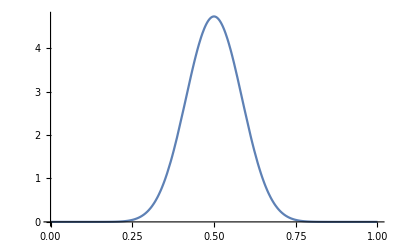

```mathematica
(*a*)
12*PDF[UniformSumDistribution[12],x]/.{x->12y}  (*生成12个UniformSumDistribution*)
Plot[12*Evaluate[PDF[UniformSumDistribution[12],x] /. {x -> y*12}], {y,0,1}]
```

```mathematica
(*b ， 两种方法*)
N[Probability[6≤x≤8, x\[Distributed] UniformSumDistribution[12]]]
N[CDF[UniformSumDistribution[12],8] -CDF[UniformSumDistribution[12],6]]
```

0.477724

0.477724

```mathematica
(*c , 两种方法*)
N[Probability[1/2≤x≤2/3, x\[Distributed] NormalDistribution[1/2,1/12]]]
N[CDF[NormalDistribution[1/2,1/12],2/3] -CDF[NormalDistribution[1/2,1/12],1/2]]
```

0.47725

0.47725

Question 3

Let Y = A + B + C + D be the sum of a random sample of size 4 from the distribution whose pdf is that of U^(1/3) where U~U(0, 1).
a. The function t1 in the notebook Lab6.nb sets up the pdf of U^(1/3). Plot it and find the mean and variance of A.
b. Find the pdf of Y, and plot the pdf of Y.
c. Calculate P(0.3≤Y≤1.5) based on the pdf of Y.
d. Approximate P(0.3≤Y≤1.5) based on the normal distribution, and see how close it is to the result of (c).

BetaDistribution[3,1]

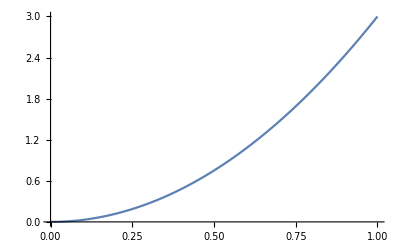

3/4

3/80

```mathematica
(*a. solution*)
(*function t1 in notebook Lab6.nb*)
t1 = TransformedDistribution[U^(1/3),U \[Distributed] UniformDistribution[]]
(*plot pdf graph*)
Plot[PDF[t1,x],{x,0,1}]
(*mean and variance*)
Mean[t1]
Variance[t1]
```

TransformedDistribution[x1+x2+x3+x4,{x1\[Distributed]BetaDistribution[3,1],x2\[Distributed]BetaDistribution[3,1],x3\[Distributed]BetaDistribution[3,1],x4\[Distributed]BetaDistribution[3,1]}]

Function[x,1/61600(415800 (-4+x)^3 Sign[-4+x]+831600 (-4+x)^4 Sign[-4+x]+665280 (-4+x)^5 Sign[-4+x]+277200 (-4+x)^6 Sign[-4+x]+67320 (-4+x)^7 Sign[-4+x]+9900 (-4+x)^8 Sign[-4+x]+880 (-4+x)^9 Sign[-4+x]+44 (-4+x)^10 Sign[-4+x]+(-4+x)^11 Sign[-4+x]-166320 (-3+x)^5 Sign[-3+x]-166320 (-3+x)^6 Sign[-3+x]-71280 (-3+x)^7 Sign[-3+x]-15840 (-3+x)^8 Sign[-3+x]-1980 (-3+x)^9 Sign[-3+x]-132 (-3+x)^10 Sign[-3+x]-4 (-3+x)^11 Sign[-3+x]+11880 (-2+x)^7 Sign[-2+x]+5940 (-2+x)^8 Sign[-2+x]+1320 (-2+x)^9 Sign[-2+x]+132 (-2+x)^10 Sign[-2+x]+6 (-2+x)^11 Sign[-2+x]-220 (-1+x)^9 Sign[-1+x]-44 (-1+x)^10 Sign[-1+x]-4 (-1+x)^11 Sign[-1+x]+x^11 Sign[x])]

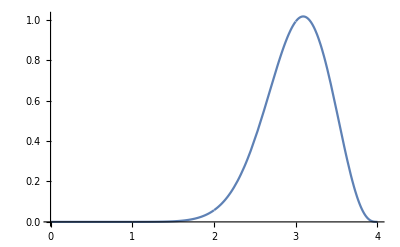

```mathematica
(*b. solution*)
(*construct distribution of Y*)
tf=TransformedDistribution[A + B + C + D,{A\[Distributed]t1,B\[Distributed]t1,C \[Distributed] t1,D \[Distributed] t1}]
ee= PDF[tf]
Plot[ee[x],{x,0,4}]
```

```mathematica
(*c. solution*)
N[CDF[tf,1.5]- CDF[tf,0.3]]
```

0.000350282

```mathematica
(*d. solution*)
Mean[tf]
Variance[tf]
N[CDF[NormalDistribution[3,√0.15],1.5]- CDF[ NormalDistribution[3,√0.15],0.3]]

(*跟正态分布结果相比，结果不是很好，因为区间[0.3, 1.5]距离中心点3太远了，所以最后得结果值很小*)
```

3

3/20

0.0000537556

## Sample lab test example

Question 2

Continuous random variable X have following pdf:
	 f(x) = 2/9 (2-x) (1+x), -1 < x < 2.
a). Find the cdf F(x) of X.
b). Find the probability P(-2<X<9/5).
c). Find the mean E(X).
d). Find the mgf M(t) = E[e^tX].
e). Find the third moment E(X^3).
f). Let Y = X^2.
	i) What are the possible values of Y?
	ii) Find the pdf g(y) of Y.

```mathematica
(*a. solution*)
Q2 = ProbabilityDistribution[2/9*(x+1)*(2-x), {x, -1, 2}]
CDF[Q2]
```

ProbabilityDistribution[2/9 (2-x) (1+x),{x,-1,2}]

Function[x,Piecewise[{{1, x≥2}, {1/27 (7+12 x+3 x^2-2 x^3), -1<x<2}, {0, True}}],Listable]

```mathematica
(*b. solution*)
CDF[Q2, 9/5] - CDF[Q2, -2]
N[%]
```

3332/3375

0.987259

```mathematica
(*c. solution*)
Mean[Q2]
```

1/2

```mathematica
(*d. solution*)
MomentGeneratingFunction[Q2, t]
```

(ⅇ^-t (4+6 t+ⅇ^(3 t) (-4+6 t)))/(9 t^3)

```mathematica
(*e. solution*)
Expectation[X^3, X \[Distributed] Q2]
```

4/5

```mathematica
(*f - ii solution*)
Y = TransformedDistribution[X^2,{X \[Distributed] Q2}]
PDF[Y]
```

TransformedDistribution[X^2,{X\[Distributed]ProbabilityDistribution[2/9 (2-x) (1+x),{x,-1,2}]}]

Function[x,Piecewise[{{(2+√x-x)/(9 √x), 1≤x<4}, {-(2 (-2+x))/(9 √x), 0<x<1}, {0, x≥4||x<0}, {Indeterminate, True}}],Listable]